```mathematica
λ=1.76375I+1;
soluciones=Solve[-2 (λ+λ^3)+(3+9 λ^2) z-12 λ z^2+(3+λ^2) z^3==0,z]
z1=z/.soluciones[[1]]
z2=z/.soluciones[[2]]
z3=z/.soluciones[[3]]
```

{{z→0.0802346+0.958759 ⅈ},{z→0.531684+0.37065 ⅈ},{z→5.8359-3.10593 ⅈ}}

0.0802346+0.958759 ⅈ

0.531684+0.37065 ⅈ

5.8359-3.10593 ⅈ

```mathematica
p[z_]:=(z^2-1)(z-λ);lp[z_]=p[z]p''[z]/p'[z]/p'[z];sp[z_]=z-1/(1-lp[z])p[z]/p'[z];
iterSch= Compile[{{z,_Complex}},sp[z]];
r1=1;r2=-1;r3=λ;
Clear[rootPosition]
rootPosition[z_]:= 
Which[Abs[z - r1] <  10.0^(-6), 3,
	       Abs[z - r2] <  10.0^(-6), 2,
	       Abs[z -r3] <  10.0^(-6), 1,
	       True, 0]
Clear[iterColorAlgorithm,colorLevel,fractalColor,plotColorFractal]
iterColorAlgorithm[iterMethod_,x_,y_,lim_] :=
Block[{z,ct,r}, z = x + y I; ct = 0;r = rootPosition[z];
While[(r==0) && (ct < lim),++ct;
z = iterMethod[z];r = rootPosition[z]
];
If[Head[r]==Which,r =0]; (* "Which" unevaluated *)
Return[N[r+ct/(lim+0.001)]]
]
colorLevelWS= Compile[{{p,_Real}},0.4*FractionalPart[p]];
fractalColorWS[p_] :=
Block[{pp = colorLevelWS[p]},
Switch[IntegerPart[p],
3, CMYKColor[0.6+pp,0.,0.,2*pp],
2, CMYKColor[0.,0.6+pp,0.,2*pp],
1, CMYKColor[0.,0.,0.6+pp,2*pp],
0, CMYKColor[0.,0.,0.,1.]
]
]
ft[min_,max_,pt_,nTicks_]:=Block[{taux,j,stepTicks=(max-min)/(nTicks-1)},
taux=Table[{pt*(j-1)/(nTicks-1)+1,min+(j-1)*stepTicks},{j,1,nTicks}]
]
plotColorFractal[iterMethod_,points_]:=
Block[{$Messages = {},
stepx=(xxMax-xxMin)/points,stepy=(yyMax-yyMin)/points},
ArrayPlot[Table[iterColorAlgorithm[iterMethod,x,y,limIterations],
{y,yyMax,1.00001*yyMin,-stepy},
{x,xxMin,1.00001*xxMax,stepx}],
FrameTicks->{ft[yyMax,yyMin,points,5],ft[xxMin,xxMax,points,5]},
PlotRange->{0,4},(* Three roots *)
ColorFunctionScaling->False,
ColorFunction->fractalColorWS
]
]
```

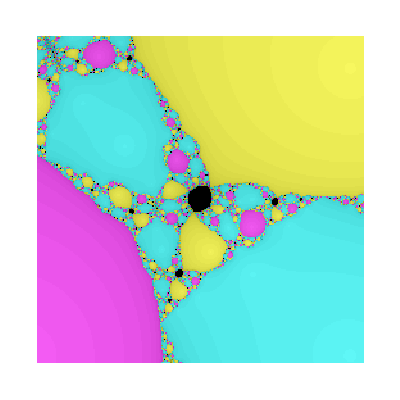

```mathematica
numberPoints =254;
limIterations=50;
xxMin=Re[z1]-1; xxMax=Re[z1]+1; yyMin=Im[z1]-1; yyMax=Im[z1]+1;
plotColorFractal[iterSch, numberPoints]
```

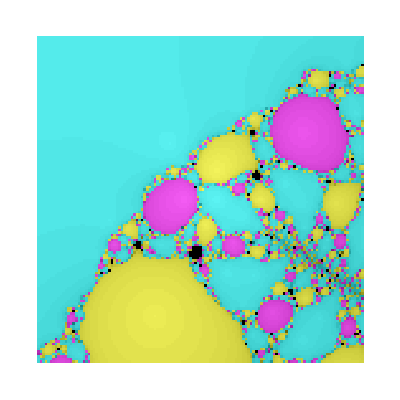

```mathematica
numberPoints =128;
limIterations=50;
xxMin=-10; xxMax=10; yyMin=-10; yyMax=10;
plotColorFractal[iterSch, numberPoints]
```

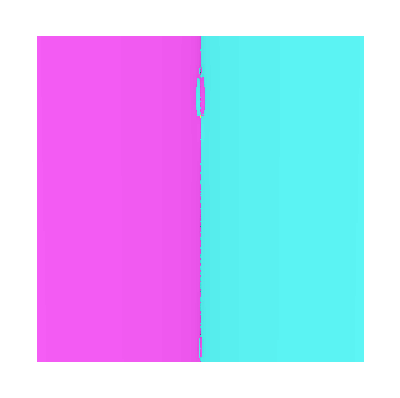

```mathematica
numberPoints =256;
limIterations=100;
xxMin=-0.25; xxMax=0.25; yyMin=0.25; yyMax=0.32;
plotColorFractal[iterSch, numberPoints]
```

```mathematica
NestList[sp,z1,100]
```

{0.0802346+0.958759 ⅈ,-0.473873+2.15609 ⅈ,3.51286+1.42998 ⅈ,0.079387+0.950003 ⅈ,-0.473249+2.15635 ⅈ,3.50958+1.43168 ⅈ,0.0789826+0.950961 ⅈ,-0.47335+2.15623 ⅈ,3.51042+1.43166 ⅈ,0.0791602+0.950808 ⅈ,-0.473341+2.15627 ⅈ,3.51025+1.43159 ⅈ,0.0791116+0.950821 ⅈ,-0.47334+2.15626 ⅈ,3.51028+1.43162 ⅈ,0.0791224+0.950823 ⅈ,-0.47334+2.15626 ⅈ,3.51028+1.43161 ⅈ,0.0791205+0.950822 ⅈ,-0.47334+2.15626 ⅈ,3.51028+1.43161 ⅈ,0.0791207+0.950822 ⅈ,-0.47334+2.15626 ⅈ,3.51028+1.43161 ⅈ,0.0791207+0.950822 ⅈ,-0.47334+2.15626 ⅈ,3.51028+1.43161 ⅈ,0.0791207+0.950822 ⅈ,-0.47334+2.15626 ⅈ,3.51028+1.43161 ⅈ,0.0791207+0.950822 ⅈ,-0.47334+2.15626 ⅈ,3.51028+1.43161 ⅈ,0.0791207+0.950822 ⅈ,-0.47334+2.15626 ⅈ,3.51028+1.43161 ⅈ,0.0791207+0.950822 ⅈ,-0.47334+2.15626 ⅈ,3.51028+1.43161 ⅈ,0.0791207+0.950822 ⅈ,-0.47334+2.15626 ⅈ,3.51028+1.43161 ⅈ,0.0791207+0.950822 ⅈ,-0.47334+2.15626 ⅈ,3.51028+1.43161 ⅈ,0.0791207+0.950822 ⅈ,-0.47334+2.15626 ⅈ,3.51028+1.43161 ⅈ,0.0791207+0.950822 ⅈ,-0.47334+2.15626 ⅈ,3.51028+1.43161 ⅈ,0.0791207+0.950822 ⅈ,-0.47334+2.15626 ⅈ,3.51028+1.43161 ⅈ,0.0791207+0.950822 ⅈ,-0.47334+2.15626 ⅈ,3.51028+1.43161 ⅈ,0.0791207+0.950822 ⅈ,-0.47334+2.15626 ⅈ,3.51028+1.43161 ⅈ,0.0791207+0.950822 ⅈ,-0.47334+2.15626 ⅈ,3.51028+1.43161 ⅈ,0.0791207+0.950822 ⅈ,-0.47334+2.15626 ⅈ,3.51028+1.43161 ⅈ,0.0791207+0.950822 ⅈ,-0.47334+2.15626 ⅈ,3.51028+1.43161 ⅈ,0.0791207+0.950822 ⅈ,-0.47334+2.15626 ⅈ,3.51028+1.43161 ⅈ,0.0791207+0.950822 ⅈ,-0.47334+2.15626 ⅈ,3.51028+1.43161 ⅈ,0.0791207+0.950822 ⅈ,-0.47334+2.15626 ⅈ,3.51028+1.43161 ⅈ,0.0791207+0.950822 ⅈ,-0.47334+2.15626 ⅈ,3.51028+1.43161 ⅈ,0.0791207+0.950822 ⅈ,-0.47334+2.15626 ⅈ,3.51028+1.43161 ⅈ,0.0791207+0.950822 ⅈ,-0.47334+2.15626 ⅈ,3.51028+1.43161 ⅈ,0.0791207+0.950822 ⅈ,-0.47334+2.15626 ⅈ,3.51028+1.43161 ⅈ,0.0791207+0.950822 ⅈ,-0.47334+2.15626 ⅈ,3.51028+1.43161 ⅈ,0.0791207+0.950822 ⅈ,-0.47334+2.15626 ⅈ,3.51028+1.43161 ⅈ,0.0791207+0.950822 ⅈ,-0.47334+2.15626 ⅈ,3.51028+1.43161 ⅈ,0.0791207+0.950822 ⅈ,-0.47334+2.15626 ⅈ}

```mathematica
NestList[sp,z2,100]
```

General::munfl: (6.42317×10^-158+0. ⅈ) (5.16197×10^-159+0.283487 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (7.13115×10^-174+0. ⅈ) (5.73093×10^-175+0.283487 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (7.91717×10^-190+0. ⅈ) (6.36262×10^-191+0.283487 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{0.531684+0.37065 ⅈ,0.858766+0.0589763 ⅈ,0.982801-0.00123532 ⅈ,0.999878-0.00018791 ⅈ,1.-1.14685×10^-8 ⅈ,1.-2.54495×10^-16 ⅈ,1.-7.39557×10^-31 ⅈ,1.-8.75812×10^-47 ⅈ,1.-9.72346×10^-63 ⅈ,1.-1.07952×10^-78 ⅈ,1.-1.19851×10^-94 ⅈ,1.-1.33061×10^-110 ⅈ,1.-1.47728×10^-126 ⅈ,1.-1.64011×10^-142 ⅈ,1.-1.82088×10^-158 ⅈ,1.-2.02159×10^-174 ⅈ,1.-2.24441×10^-190 ⅈ,1.-2.4918×10^-206 ⅈ,1.-2.76645×10^-222 ⅈ,1.-3.07138×10^-238 ⅈ,1.-3.40992×10^-254 ⅈ,1.-3.78577×10^-270 ⅈ,1.-4.20305×10^-286 ⅈ,1.-4.66632×10^-302 ⅈ,1.-5.18065×10^-318 ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ}

```mathematica
NestList[sp,z3,100]
```

{5.8359-3.10593 ⅈ,0.292494+0.70382 ⅈ,11.1672-6.36534 ⅈ,0.303234+0.676716 ⅈ,4.07513-2.09029 ⅈ,0.304672+0.683276 ⅈ,4.29305-2.85954 ⅈ,0.303306+0.702484 ⅈ,5.14005-7.31534 ⅈ,0.2691+0.691522 ⅈ,6.51843+2.57134 ⅈ,0.34238+0.786167 ⅈ,-2.17774+0.19534 ⅈ,-0.527881-0.122937 ⅈ,-0.830451-0.206765 ⅈ,-1.04086-0.0515654 ⅈ,-0.999625+0.00339938 ⅈ,-1.00001+4.8059×10^-6 ⅈ,-1.-7.37279×10^-11 ⅈ,-1.-5.61824×10^-22 ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ}